## Mathematica Project for Calculus 3 (MA2733-02) Contributors: Brody Pennington (BGP99)

## Problem 1

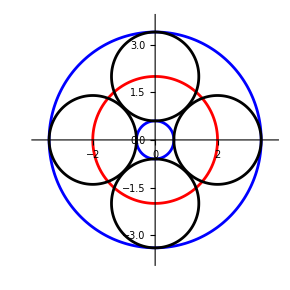

```mathematica
ParametricPlot[
{
{.6Cos[t], .6Sin[t]}, 
{2Cos[t], 2Sin[t]},
{3.4Cos[t], 3.4Sin[t]},

{2Cos[0] + 1.4Cos[t], 2Sin[0]+1.4Sin[t]},
{2Cos[π/2] + 1.4Cos[t], 2Sin[π/2]+1.4Sin[t]},
{2Cos[π] + 1.4Cos[t], 2Sin[π]+1.4Sin[t]},
{2Cos[(3π)/2] + 1.4Cos[t], 2Sin[(3π)/2]+1.4Sin[t]}
},
{t, 0, 2π},
PlotRange->{{-3.8, 3.8}, {-3.8, 3.8}},
PlotStyle->{
{Blue},
{Red},
{Blue},  
{Black}, 
{Black},
{Black},
{Black},
},
AspectRatio->1
]
```

## Problem 2

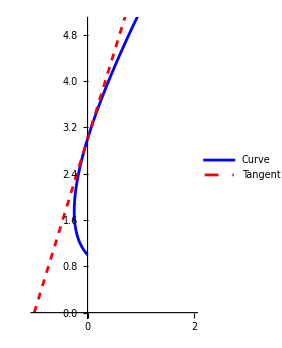

```mathematica
xExpr=t^2-t;
yExpr=t^2+t+1;
pointX=xExpr/. t->1;
pointY=yExpr/. t->1;
dxdt=D[xExpr,t];
dydt=D[yExpr,t];
slope=(dydt/dxdt)/. t->1;
tangentLineExpr=slope*(x-pointX)+pointY;
Show[
ParametricPlot[
	{xExpr/. t->t,yExpr/. t->t},
	{t,0,2},
	PlotRange->{{-1,2},{0,5}},
	PlotStyle->Blue,
	PlotLegends->{"Curve"}
],
Plot[
	tangentLineExpr,
	{x,-1,2},
	PlotStyle->{Red,Dashed},
	PlotLegends->{"Tangent Line"}
]
]
```

## Problem 3

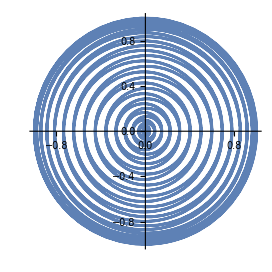

```mathematica
PolarPlot[
Cos[θ/64]^2, {θ, 0, 128π},
PlotRange->All
]
```

## Problem 4

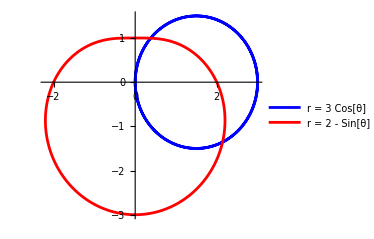

{2 π+2 ArcTan[1/5 (1-√6)],2 ArcTan[1/5 (1+√6)]}

(6 √6)/5

```mathematica
PolarPlot[
{3 Cos[θ],2-Sin[θ]},
{θ,0,2 Pi},
PlotLegends->{"r = 3 Cos[θ]","r = 2 - Sin[θ]"},
PlotStyle->{Blue,Red},
PlotRange->All
]
r1[θ_]:=3 Cos[θ];
r2[θ_]:=2-Sin[θ];
solutions=Solve[3 Cos[θ]==2-Sin[θ]&&0<=θ<=2 Pi,θ];
a=θ/. solutions[[1]];
b=θ/. solutions[[2]];
{a,b}
area=(1/2) Integrate[(r1[θ]^2-r2[θ]^2),{θ,a,b}]
```

## Problem 5

```mathematica
ContourPlot3D[
-x^2+y^2-z^2==1,
{x,-3,3},{y,-3,3},{z,-3,3},
PlotRange->All,
Mesh->None,
PlotPoints->50,
AxesLabel->{"x","y","z"},
Boxed->False,
PlotLabel->"Hyperboloid of One Sheet"
]
ContourPlot3D[
(3 x^2+3 z^2+25 y^2-1)^3+4 x^2 z^3+(6/25) y^2 z^3==0,
{x,-2,2},{y,-2,2},{z,-2,2},
PlotRange->All,
Mesh->None,
PlotPoints->50,
AxesLabel->{"x","y","z"},
Boxed->False,
PlotLabel->"Complex Surface"
]
```

-Graphics3D-

-Graphics3D-

## Problem 6

```mathematica
ClearAll["Global`*"]
r[t_]:={t/(t^2+1), Sqrt[t-3], 3Cos[t/2]}
rPrime = D[r[t], t]
rDoublePrime = D[r[t], {t, 2}]
T = FullSimplify[rPrime/Sqrt[rPrime.rPrime]]
crossProduct = FullSimplify[Cross[rPrime, rDoublePrime]]
```

{-(2 t^2)/((1+t^2)^2)+1/(1+t^2),1/(2 √(-3+t)),-3/2 Sin[t/2]}

{-(4 t)/((1+t^2)^2)+t ((8 t^2)/((1+t^2)^3)-2/((1+t^2)^2)),-1/(4 (-3+t)^(3/2)),-3/4 Cos[t/2]}

{-(2 (-1+t^2))/((1+t^2)^2 √(1/(-3+t)+(4 (-1+t^2)^2)/((1+t^2)^4)+9 Sin[t/2]^2)),1/(√(-3+t) √(1/(-3+t)+(4 (-1+t^2)^2)/((1+t^2)^4)+9 Sin[t/2]^2)),-(3 Sin[t/2])/(√(1/(-3+t)+(4 (-1+t^2)^2)/((1+t^2)^4)+9 Sin[t/2]^2))}

{-(3 ((-3+t) Cos[t/2]+Sin[t/2]))/(8 (-3+t)^(3/2)),-(3 (-1+t^4) Cos[t/2]+12 t (-3+t^2) Sin[t/2])/(4 (1+t^2)^3),(-1-3 t (12+t (-4+(-4+t) t)))/(4 (-3+t)^(3/2) (1+t^2)^3)}

## Problem 7

```mathematica
ClearAll["Global`*"]
r[t_]:={t^4,t^2,t^3}
ParametricPlot3D[
r[t],{t,0,2},
AxesLabel->{"x","y","z"},
Boxed->False
]
rPrime[t_]:=D[r[t],t]
magR[t_]:=Sqrt[rPrime[t].rPrime[t]]
lengthOfCurve=NIntegrate[magR[t],{t,0,2},PrecisionGoal->6]
```

-Graphics3D-

18.6833

## Problem 8

```mathematica
ClearAll["Global`*"]
r[t_]:={Sin[t],Cos[t],Cos[3 t]}
ParametricPlot3D[r[t],{t,0,2 Pi},AxesLabel->{"x","y","z"},Boxed->False,PlotRange->All]
rPrime[t_]:=Evaluate[D[r[t],t]]
rPrime2[t_]:=Evaluate[D[rPrime[t],t]]
magNum[t_]:=Norm[Cross[rPrime[t],rPrime2[t]]]
magDenom[t_]:=Norm[rPrime[t]]^3
curve[t_]:=magNum[t]/magDenom[t]
(*sin(t)=1=pi/2*)
curveAtPoint=curve[Pi/2]
```

-Graphics3D-

1/10

## Problem 9

```mathematica
ClearAll["Global`*"]
r[t_]:={t^2,Log[t],2t}
(*velocity vector-> (dr/dt)*)
velocity=Simplify[D[r[t],t]]
(*T vector*)
Tmag=Simplify[Sqrt[velocity.velocity]]
T[t_]:=Simplify[velocity/Tmag]
(*acceleration vector-> (d.b2r/dt.b2)*)
acceleration=Simplify[D[velocity,t]]
(*N vector*)
N1[t_]:=Simplify[acceleration-(acceleration.T[t])*T[t]]
Nmag=Simplify[Sqrt[N1[1].N1[1]]]
N2[t_]:=Simplify[N1[t]/Nmag]
(*B vector*)
B[t_]:=Simplify[Cross[T[t],N2[t]]]
(*t=1*)
t0=1;
Print[""]
Print["At t = 1:"]
Print["T = ",Simplify[T[t0]]]
Print["N = ",Simplify[N2[t0]]]
Print["B = ",Simplify[B[t0]]]
```

{2 t,1/t,2}

√(4+1/t^2+4 t^2)

{2,-1/t^2,0}

2 √(1/t^2)

At t = 1:

T = {(2 t)/(√(4+1/t^2+4 t^2)),1/(t √(4+1/t^2+4 t^2)),2/(√(4+1/t^2+4 t^2))}

N = {2/(√(1/t^2) (1+2 t^2)),-2/(√(1/t^2) (1+2 t^2)),(2-4 t^2)/(2 √(1/t^2) (t+2 t^3))}

B = {(√(1/t^2))/(√(4+1/t^2+4 t^2)),2/(√(1/t^2) √(4+1/t^2+4 t^2)),-(2 √(1/t^2) t)/(√(4+1/t^2+4 t^2))}

## Problem 10

1-x^4/2+x^8/24

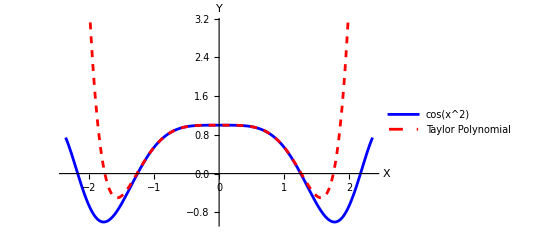

0.815705

0.815781

At x = π/4:

Actual value = 0.815705

Taylor polynomial value = 0.815781

```mathematica
ClearAll["Global`*"]
(*Taylor Series for Cos(x^2)*)
series = Normal[Series[Cos[x^2], {x, 0, 10}]]
Plot[{Cos[x^2], series}, {x, -3Pi/4, 3Pi/4},
PlotLegends->{"cos(x^2)", "Taylor Polynomial"},
PlotStyle->{{Blue}, {Red, Dashed}},
AxesLabel->{"X", "Y"}
]
actualValue = N[Cos[(Pi/4)^2]]
taylorValue=N[series/. x->Pi/4]
Print["At x = π/4:"]
Print["Actual value = ",actualValue]
Print["Taylor polynomial value = ",taylorValue]
```